```mathematica
allGraphs2[0]//Keys
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull}

```mathematica
allGraphs4[0, "parents"]//Flatten
```

{}

```mathematica
Map[ShowGraph[allGraphs5,#]&,{19683,39366,6561,13122,2187,4374,729,1458,243,486,81,162,27,54,9,18,3,6,1,2}]
```

{-Graphics-19683,-Graphics-39366,-Graphics-6561,-Graphics-13122,-Graphics-2187,-Graphics-4374,-Graphics-729,-Graphics-1458,-Graphics-243,-Graphics-486,-Graphics-81,-Graphics-162,-Graphics-27,-Graphics-54,-Graphics-9,-Graphics-18,-Graphics-3,-Graphics-6,-Graphics-1,-Graphics-2}

```mathematica
Map[ShowGraph[allGraphs5,#]&,allGraphs5[0, "children"]//Flatten]
```

KeyExistsQ::invrl: The argument 19683[<|0 -> <|signature -> 0, <<19>>, colotree -> t12345 + t1234x5 + t123x45 + t123x4x5 + t12x345 + <<8>> + t1x2x34x5 + t1x2x3x45 + t1x2x3x4x5|>, <<1894>>|>] is not a valid Association or a list of rules.

KeyExistsQ::invrl: The argument 39366[<|0 -> <|signature -> 0, <<19>>, colotree -> t12345 + t1234x5 + t123x45 + t123x4x5 + t12x345 + <<8>> + t1x2x34x5 + t1x2x3x45 + t1x2x3x4x5|>, <<1894>>|>] is not a valid Association or a list of rules.

General::stop: Further output of KeyExistsQ::invrl will be suppressed during this calculation.

$Aborted

```mathematica
Clear[DoIt];DoIt[all_]:=DoIt[all]=Block[{result=Association[], changed=True},
Monitor[
Table[
result[row]=Association[];
Table[
result[row,col]=Infinity
,
{col ,Keys[all]}]
,{row ,Keys[all]}];
Table[
result[row,row]=0;
Table[

result[row,col]=1;
result[col,row]=1
,
{col ,Flatten[all[row,"children"]]}]
,{row ,Keys[all]}];
Table[
Table[

result[row,col]=1;
result[col,row]=1
,
{col ,Flatten[all[row,"parents"]]}]
,{row ,Keys[all]}];
While[changed,
changed=False;
Table[
Table[
Table[
If[result[row,via]>result[row,col]+result[col,via],
result[row,via]=result[row,col]+result[col,via];
changed=True;
]
,
{via ,Keys[all]}]
,
{col ,Keys[all]}]
,{row ,Keys[all]}]
];
result,
{row,col,via}]
]
```

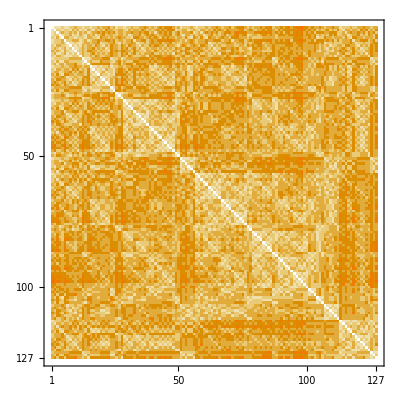

```mathematica
d=DoIt[]; MatrixPlot[d]
```

```mathematica
Table[DoIt[all];,{all,{allGraphs2,allGraphs3, allGraphs4}}]
```

{Null,Null,Null}

```mathematica
TableForm[Table[Tally[Flatten[DoIt[all]]],{all,{allGraphs2,allGraphs3, allGraphs4}}], TableDepth->2]
```

{0,3} | {1,4} | {2,2} |  |  |  | 
{0,15} | {1,60} | {2,92} | {3,56} | {4,2} |  | 
{0,127} | {1,1084} | {2,3870} | {3,6770} | {4,3872} | {5,402} | {6,4}

```mathematica
Table[DoIt[all];,{all,{allGraphs2,allGraphs3, allGraphs4}}]
```

{Null,Null,Null}

```mathematica
vec=With[{lookup=DoIt[allGraphs4]},
Flatten[Table[{row,col,lookup[row,col]},{row,Keys[lookup]},{col,Keys[lookup]}],1]]
```

```mathematica
Select[vec,#[[1]]<#[[2]]&&#[[3]]==6&]
```

{{0,364,6},{364,728,6}}

```mathematica
allGraphs4[728,"parents"]//DeleteDuplicates
```

{666,546,488,218,168,72,26}

```mathematica
ShowGraph[allGraphs4,364]
```

-Graphics-364

```mathematica
Table[ShowGraph[allGraphs4,k],{k,allGraphs4[364,"parents"]//Flatten//DeleteDuplicates}]
```

{-Graphics-363,-Graphics-361,-Graphics-355,-Graphics-337,-Graphics-283,-Graphics-121}

```mathematica
DoIt[allGraphs4][0,728]
```

3

```mathematica
DoIt[allGraphs4][728,364]
```

6